{{x→-(d (-1+ⅇ^(ⅈ p) r))/(1+ⅇ^(ⅈ p) r)}}

{{x→-(d (-1+ⅇ^(ⅈ p) r))/(1+ⅇ^(ⅈ p) r)}}

{{y→-(ⅈ d (-1+ⅇ^(ⅈ p) r))/(1+ⅇ^(ⅈ p) r)}}

{{y→(ⅈ d (-1+ⅇ^(ⅈ p) r))/(1+ⅇ^(ⅈ p) r)}}

{-0.338459-0.1168 ⅈ}

{-0.338459-0.1168 ⅈ}

{0.1168-0.338459 ⅈ}

{-0.1168+0.338459 ⅈ}

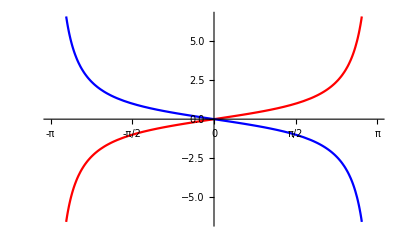

```mathematica
(*---no microstrip ---*)
Clear["Global`*"]
(*two-trace no ground general phase*)
R = r*L*Exp[I*p]; L=1;
Bx= -L*(y)/((x+d)^2+(y)^2)-R*(y)/((x-d)^2+(y)^2);
By= +L*(x+d)/((x+d)^2+(y)^2)+R*(x-d)/((x-d)^2+(y)^2);
s2tpx= Solve[Bx+I*By==0/.y->0, x]
s2tmx= Solve[Bx-I*By==0/.y->0, x]
s2tpy= Solve[Bx+I*By==0/.x->0, y]
s2tmy= Solve[Bx-I*By==0/.x->0, y]
N[x/.s2tpx/.d->1/.r->2/.p->Pi/12]
N[x/.s2tmx/.d->1/.r->2/.p->Pi/12]
N[y/.s2tpy/.d->1/.r->2/.p->Pi/12]
N[y/.s2tmy/.d->1/.r->2/.p->Pi/12]
(*uhh... these are simply tangents of the half angle when r==1...euler trig... *)
ptan[p_] :=+Tan[p/2]*1; (*r,d==1*)
mtan[p_] :=-Tan[p/2]*1; (*r,d==1*)
Plot[{ptan[p],mtan[p]}, {p,-Pi,Pi},Ticks->{{-π, -3*π/4,-π/2,-π/4,0,π/4, π/2, 3*π/4, π},Automatic},PlotStyle -> {Red, Blue}]
```

{{x→-(d (-1+ⅇ^(ⅈ p) r)+√(-4 d^2 ⅇ^(ⅈ p) r-(s+ⅇ^(ⅈ p) r s)^2))/(1+ⅇ^(ⅈ p) r)},{x→(d-d ⅇ^(ⅈ p) r+√(-4 d^2 ⅇ^(ⅈ p) r-(s+ⅇ^(ⅈ p) r s)^2))/(1+ⅇ^(ⅈ p) r)}}

{{x→-(d (-1+ⅇ^(ⅈ p) r)+√(-4 d^2 ⅇ^(ⅈ p) r-(s+ⅇ^(ⅈ p) r s)^2))/(1+ⅇ^(ⅈ p) r)},{x→(d-d ⅇ^(ⅈ p) r+√(-4 d^2 ⅇ^(ⅈ p) r-(s+ⅇ^(ⅈ p) r s)^2))/(1+ⅇ^(ⅈ p) r)}}

{{y→-(ⅈ d (-1+ⅇ^(ⅈ p) r)+√(4 d^2 ⅇ^(ⅈ p) r+(s+ⅇ^(ⅈ p) r s)^2))/(1+ⅇ^(ⅈ p) r)},{y→(-ⅈ d (-1+ⅇ^(ⅈ p) r)+√(4 d^2 ⅇ^(ⅈ p) r+(s+ⅇ^(ⅈ p) r s)^2))/(1+ⅇ^(ⅈ p) r)}}

{{y→(ⅈ d (-1+ⅇ^(ⅈ p) r)-√(4 d^2 ⅇ^(ⅈ p) r+(s+ⅇ^(ⅈ p) r s)^2))/(1+ⅇ^(ⅈ p) r)},{y→(ⅈ d (-1+ⅇ^(ⅈ p) r)+√(4 d^2 ⅇ^(ⅈ p) r+(s+ⅇ^(ⅈ p) r s)^2))/(1+ⅇ^(ⅈ p) r)}}

{-0.309779+1.26157 ⅈ,-0.367139-1.49517 ⅈ}

{-0.309779+1.26157 ⅈ,-0.367139-1.49517 ⅈ}

{-1.26157-0.309779 ⅈ,1.49517-0.367139 ⅈ}

{-1.49517+0.367139 ⅈ,1.26157+0.309779 ⅈ}

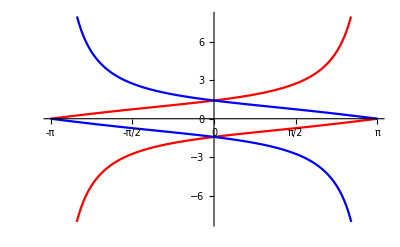

```mathematica
(*two-microstrip any phase *)
Clear["Global`*"]
R = r*L*Exp[I*p];
Bx= -L*(y-s)/((x+d)^2+(y-s)^2)-R*(y-s)/((x-d)^2+(y-s)^2) +L*(y+s)/((x+d)^2+(y+s)^2)+R*(y+s)/((x-d)^2+(y+s)^2);
By= +L*(x+d)/((x+d)^2+(y-s)^2)+R*(x-d)/((x-d)^2+(y-s)^2) -L*(x+d)/((x+d)^2+(y+s)^2)-R*(x-d)/((x-d)^2+(y+s)^2);
s2mpx=Simplify[Solve[Bx+I*By==0/. y->0, x]]
s2mmx=Simplify[Solve[Bx-I*By==0/. y->0, x]]
s2mpy=Simplify[Solve[Bx+I*By==0/. x->0, y]]
s2mmy=Simplify[Solve[Bx-I*By==0/. x->0, y]]
N[x/.s2mpx/.d->1/.s->1/.r->2/.p->Pi/12]
N[x/.s2mmx/.d->1/.s->1/.r->2/.p->Pi/12]
N[y/.s2mpy/.d->1/.s->1/.r->2/.p->Pi/12]
N[y/.s2mmy/.d->1/.s->1/.r->2/.p->Pi/12]
plusv3[p_] :=Tan[p/2]+Sqrt[1+Sec[p/2]^2]
plusv4[p_] :=Tan[p/2]-Sqrt[1+Sec[p/2]^2]
minusv3[p_] :=-Tan[p/2]-Sqrt[1+Sec[p/2]^2]
minusv4[p_] :=-Tan[p/2]+Sqrt[1+Sec[p/2]^2]
Plot[{plusv3[p],plusv4[p],minusv3[p],minusv4[p]},{p,-Pi, Pi},Ticks->{{-π, -3*π/4,-π/2,-π/4,0,π/4, π/2, 3*π/4, π},Automatic},PlotStyle -> {Red, Red, Blue, Blue}]
```

```mathematica
(*--- Three - strip ---*)
(*3- wire general *)
Clear["Global`*"]
M = r*Exp[I*p];R=1; L=1;
Bx= -L*(y)/((x+d)^2+(y)^2)-M*(y)/(x^2+(y)^2)-R*(y)/((x-d)^2+(y)^2);
By= +L*(x+d)/((x+d)^2+(y)^2)+M*(x)/(x^2+(y)^2)+R*(x-d)/((x-d)^2+(y)^2) ;
s3tpx = Solve[Bx+I*By==0/.y->0, x]
s3tmx = Solve[Bx-I*By==0/.y->0, x]
s3tpy = Solve[Bx+I*By==0/.x->0, y]
s3tmy = Solve[Bx-I*By==0/.x->0, y]
N[x/.s3tpx/.d->1/.r->2/.p->13Pi/12]
N[x/.s3tmx/.d->1/.r->2/.p->13Pi/12]
N[y/.s3tpy/.d->1/.r->2/.p->13Pi/12]
N[y/.s3tmy/.d->1/.r->2/.p->13Pi/12]
```

{{x→-(d ⅇ^((ⅈ p)/2) √r)/(√(2+ⅇ^(ⅈ p) r))},{x→(d ⅇ^((ⅈ p)/2) √r)/(√(2+ⅇ^(ⅈ p) r))}}

{{x→-(d ⅇ^((ⅈ p)/2) √r)/(√(2+ⅇ^(ⅈ p) r))},{x→(d ⅇ^((ⅈ p)/2) √r)/(√(2+ⅇ^(ⅈ p) r))}}

{{y→-(ⅈ d ⅇ^((ⅈ p)/2) √r)/(√(2+ⅇ^(ⅈ p) r))},{y→(ⅈ d ⅇ^((ⅈ p)/2) √r)/(√(2+ⅇ^(ⅈ p) r))}}

{{y→-(ⅈ d ⅇ^((ⅈ p)/2) √r)/(√(2+ⅇ^(ⅈ p) r))},{y→(ⅈ d ⅇ^((ⅈ p)/2) √r)/(√(2+ⅇ^(ⅈ p) r))}}

{1.4715-1.29047 ⅈ,-1.4715+1.29047 ⅈ}

{1.4715-1.29047 ⅈ,-1.4715+1.29047 ⅈ}

{1.29047+1.4715 ⅈ,-1.29047-1.4715 ⅈ}

{1.29047+1.4715 ⅈ,-1.29047-1.4715 ⅈ}

```mathematica
(* THREE microstrip *)
Clear["Global`*"]
M = r*Exp[I*p];R=1; L=1;
Bx= -L*(y-s)/((x+d)^2+(y-s)^2)-M*(y-s)/(x^2+(y-s)^2)-R*(y-s)/((x-d)^2+(y-s)^2) +L*(y+s)/((x+d)^2+(y+s)^2)+M*(y+s)/(x^2+(y+s)^2)+R*(y+s)/((x-d)^2+(y+s)^2);
By= +L*(x+d)/((x+d)^2+(y-s)^2)+M*(x)/(x^2+(y-s)^2)+R*(x-d)/((x-d)^2+(y-s)^2) +-L*(x+d)/((x+d)^2+(y+s)^2)-M*(x)/(x^2+(y+s)^2)-R*(x-d)/((x-d)^2+(y+s)^2);
s3mpx = Simplify[Solve[Bx+I*By==0/.y->0, x]]
s3mmx = Simplify[Solve[Bx-I*By==0/.y->0, x]]
s3mpy = Simplify[Solve[Bx+I*By==0/.x->0, y]]
s3mmy = Simplify[Solve[Bx-I*By==0/.x->0, y]]
N[x/.s3mpx/.d->1/.s->1/.r->2/.p->13Pi/12]
N[x/.s3mmx/.d->1/.s->1/.r->2/.p->13Pi/12]
N[y/.s3mpy/.d->1/.s->1/.r->2/.p->13Pi/12]
N[y/.s3mmy/.d->1/.s->1/.r->2/.p->13Pi/12]
```

{{x→-√(-(d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{x→√(-(d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{x→-√((d^2 (-1+ⅇ^(ⅈ p) r)-2 s^2-ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{x→√((d^2 (-1+ⅇ^(ⅈ p) r)-2 s^2-ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))}}

{{x→-√(-(d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{x→√(-(d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{x→-√((d^2 (-1+ⅇ^(ⅈ p) r)-2 s^2-ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{x→√((d^2 (-1+ⅇ^(ⅈ p) r)-2 s^2-ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))}}

{{y→-√((d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2-√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{y→√((d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2-√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{y→-√((d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{y→√((d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))}}

{{y→-√((d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2-√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{y→√((d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2-√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{y→-√((d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))},{y→√((d^2 (1-ⅇ^(ⅈ p) r)+2 s^2+ⅇ^(ⅈ p) r s^2+√(-d^2 (d^2 (-1+4 ⅇ^(ⅈ p) r)+4 ⅇ^(ⅈ p) r (2+ⅇ^(ⅈ p) r) s^2)))/(2+ⅇ^(ⅈ p) r))}}

{-2.21952+2.64746 ⅈ,2.21952-2.64746 ⅈ,-0.795937-0.225241 ⅈ,0.795937+0.225241 ⅈ}

{-2.21952+2.64746 ⅈ,2.21952-2.64746 ⅈ,-0.795937-0.225241 ⅈ,0.795937+0.225241 ⅈ}

{-0.225241+0.795937 ⅈ,0.225241-0.795937 ⅈ,-2.64746-2.21952 ⅈ,2.64746+2.21952 ⅈ}

{-0.225241+0.795937 ⅈ,0.225241-0.795937 ⅈ,-2.64746-2.21952 ⅈ,2.64746+2.21952 ⅈ}